```mathematica
Manipulate[Range[n], {n,1,5,1}]
```

```mathematica
Table[Range[n], {n,1,5,1}]
```

{{1},{1,2},{1,2,3},{1,2,3,4},{1,2,3,4,5}}

pick!할 수 있다.

```mathematica
Table[Style["ABC",50,c],{,{Red, Green, Blue}}]
```

{Style[ABC,50,c],Style[ABC,50,c],Style[ABC,50,c]}

```mathematica
Manipulate[Style["ABC", 50, c], {c, {Red, Green, Blue}}]
```

```mathematica
Manipulate[BarChart[{x,6,2x,12,3(7-x), 18}],{x,1,6}]
```

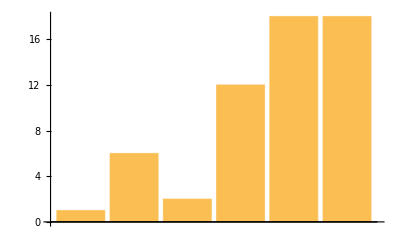
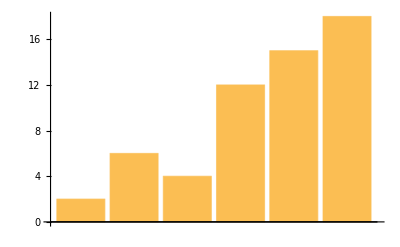
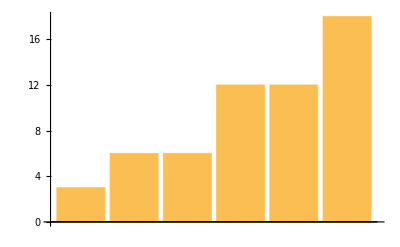
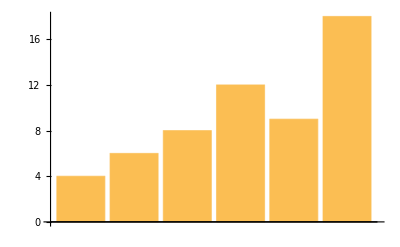
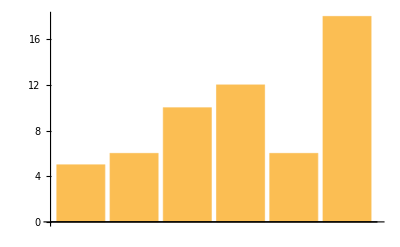
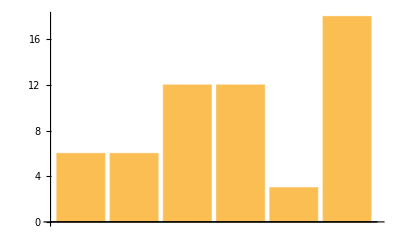

```mathematica
Table[BarChart[{x,6,2x,12,3(7-x), 18}],{x,1,6}]
```

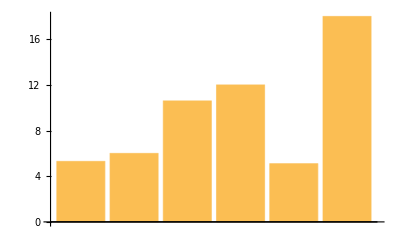

```mathematica
BarChart[{5.3,6,2*5.3,12,3(7-5.3),18}]
```

```mathematica
Manipulate[BarChart[{x,6,2*x,12,3(7-x),18}],{x,1,6}]
```

```mathematica
BarChart[{5.3,6,2*5.3,12,3(7-5.3),18}]
```

-Graphics-

```mathematica
Manipulate[BarChart[{5.3,6,2*5.3,12,3(7-5.3)}],{x,1,6}]
```

```mathematica
Manipulate[Graphics[Style[RegularPolygon[n],Hue[h]]],{n,5,20,1},{h,0,1}]
```

```mathematica
Manipulate[Graphics[Style[RegularPolygon[n],c]],{n,5,20,1},{c,{Red, Yellow, Green, Blue, Black}}]
```

```mathematica
Manipulate[Graphics[Style[RegularPolygon[n],c]],{n,5,20,1},{c,ColorSetter}]
```

Vocabulary

```mathematica
?Manipulate
```

```mathematica
Manipulate[anything, {n,0,10,1}]
```

```mathematica
Manipulate[anything, {x,0, 10}]
```

```mathematica
Manipulate[anything, {c,{Red, Yellow, Blue}}]
```

--------------------------------------------------------------------------------

```mathematica
Manipulate[Graphics[Style[Disk[], Hue[h]]], {h,0,1}]
```

```mathematica
Manipulate[Graphics[Style[Disk[], Hue[hue, saturation, brightness]]],{hue,0,1},{saturation,0,1},{brightness,0,1}]
```